# On a four-dimensional oncolytic Virotherapy model (ϵ=0)

This Mathematica Notebook is a supplementary material to the paper “On a three-dimensional and two four-dimensional
oncolytic viro-therapy models”. It contains some of the calculations and illustrations appearing in the paper concerning the section on 4 dimensional model.

### Section 3 : Four-dim viro-therapy model with Logistic growth when ϵ>0 and ϵ=0

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];
Clear["K"];
(*Some aliases*)
Format[βy]=Subscript[β,y];Format[βv]=Subscript[β,v];Format[βz]=Subscript[β,z];


Unprotect[Power];
Power[0,0]=1;
Protect[Power];

par={b,β,λ,δ,βy, βv,βz,c,γ,K,ϵ};
cp=Join[Thread[Drop[par,{1}]>0],{b>1}];
cKga1={K->1,γ->1};
cep1={ϵ->1};cep0={ϵ->0};
R0=b β K/(β K+δ)(* Reproduction number*);
cnT17={βv->0.16, βy->0.48,K->1,γ->1,b->9,β->0.11,λ->0.36,δ->0.2,βz->0.6, c->0.036};
(*Numerical values of Tian 17 after dimensionalization*)

(****** Four dim Deterministic  epidemic model with Logistic growth ****)
x1=λ  x(1-(x+y)/K)-   β x v ;
y1=β x v -βy y z- γ y;
v1=-β x v - βv  v z+ b  γ y - δ v;
z1=z(βz  y - c z^ϵ);
ye=c/βz; vM=λ(1-ye)/β;vMN=vM/.cnT17;
dyn={x1,y1,v1,z1};
dynS=dyn//.cKga1;
dyn3={x1,y1,v1}/.z->0;(*3dim case used for E* *)
dyn3S=dyn3//.cKga1;
Print[" (x'
y'
v'
z')=",dyn//FullSimplify//MatrixForm, "  the reparametrized model is (x'
y'
v'
z')=",
 dynS//FullSimplify//MatrixForm]
Print["b0=",b0=b/.Apart[Solve[R0==1,b][[1]]//FullSimplify]]
b0S=b0//.cKga1;
(*****Fixed points of Tian17 using the scaling when K=1, γ=1***)

fv=(ye (b-1)-v δ); gv=(ye βy+v βv); hv=(1-ye-v β/λ);

Print["xe= ",xe=hv, " , ye=", ye," , ze =", ze=fv/gv]

Pv=Numerator[Together[v β xe-ye (1+βy fv/gv)]]/(-βz^2 β^2 βv);
Print["P(v)=",pc=Collect[Together[Pv],v]," coefs are"]
coP=CoefficientList[pc,v]//Simplify

(***Fixed point when z->0**)
eq=Thread[dyn3=={0,0,0}];
sol=Solve[eq,{x,y,v}]//FullSimplify;
Es={x,y,v}/.sol[[3]];(*Endemic point with z=0*);
Print[" Endemic point with z=0 is E*=",Es//FullSimplify]
EsS=Es/.cKga1//FullSimplify(* E* when K=γ=1***)
Print["Check: when K=γ=1, E*=",EsS]

bn=b/.Solve[EsS[[2]]==ye,b]; bnn=bn/.cnT17;
Print["y*/ye="]
EsS[[2]]/ye//FullSimplify
Print["(b1,b2)="]
bn//FullSimplify

bcn=b/.Solve[EsS[[2]][[1]]==ye,b];
bcnn=bn/.cnT17;

Dis=Chop[Collect[Discriminant[Numerator[Pv],v],b]];
solb=Solve[Dis==0,b];
jacS=Grad[dynS,{x,y,v,z}]//FullSimplify;
Print["Jacobian"]
jacS//MatrixForm
Print["Jacobian at E_K "]
jacK=FullSimplify[jacS/.Join[sol[[2]],{z->0}],Assumptions->ϵ>=0];
jacK//MatrixForm
Print["Jacobian at E_* when K>1"]
jacEs=FullSimplify[jacS/.Join[sol[[3]],{z->0}],Assumptions->ϵ>=0](*when K>0*);
jacEs//MatrixForm

PR=Solve[Pv==0,v,Cubics->False](*//ComplexExpand[#,TargetFunctions->{Re,Im}]&*);
 vn=v/.PR[[1]]; vp=v/.PR[[3]];vi=v/.PR[[2]];
Ep={xe,ye,v,ze}/.v->vp;
Ei={xe,ye,v,ze}/.v->vi;

JEi=jacS//.{x->xe,y->ye,v->vi,z->ze};
JEp=jacS//.{x->xe,y->ye,v->vp,z->ze};
JEm=jacS//.{x->xe,y->ye,v->vn,z->ze};
jacEs1=jacEs/.cKga1;
Print["Tr[J[E*]] corresponding to 4 dim model when K=γ=1 is "]
Tr[jacEs1]
Print["Tr[J[E*]] >0 iff"]
Reduce[Join[{(Tr[jacEs1]/.ϵ->0)>0},Drop[cp,{9,10}]],Drop[par,{10,11}]]//FullSimplify
bc2=b/.solb[[1]]//FullSimplify;
bc1=b/.solb[[2]]//FullSimplify;
Print["b1*=", bc1]
Print[" b2*=", bc2]
(*(-1+(b δ)/(1-b)-c-(δ λ)/((-1+b) β)+δ/((-1+b) β)((b λ(Rz-1) βz)/(λ(b-Rz)+(-1+b) γ Rz)))*)
```

(x'
y'
v'
z')=(-v x β+x (1-(x+y)/K) λ
v x β-y (z β_y+γ)
b y γ-v (x β+z β_v+δ)
z (-c z^ϵ+y β_z))  the reparametrized model is (x'
y'
v'
z')=(-x (v β+(-1+x+y) λ)
v x β-y (1+z β_y)
b y-v (x β+z β_v+δ)
z (-c z^ϵ+y β_z))

b0=1+δ/(K β)

xe= 1-c/β_z-(v β)/λ , ye=c/β_z , ze =(((-1+b) c)/β_z-v δ)/(v β_v+(c β_y)/β_z)

P(v)=v^3+(b c^2 β_y λ)/(β^2 β_v β_z^2)+(v^2 (c β^2 β_y β_z+c β β_v β_z λ-β β_v β_z^2 λ))/(β^2 β_v β_z^2)+(v (c^2 β β_y λ+c β_v β_z λ-c β β_y β_z λ-c β_y β_z δ λ))/(β^2 β_v β_z^2) coefs are

{(b c^2 β_y λ)/(β^2 β_v β_z^2),(c (c β β_y+β_z (β_v-β_y (β+δ))) λ)/(β^2 β_v β_z^2),(c β β_y+c β_v λ-β_v β_z λ)/(β β_v β_z),1}

Endemic point with z=0 is E*={δ/((-1+b) β),(((-1+b) K β-δ) δ λ)/((-1+b) β ((-1+b) K β γ+δ λ)),(γ ((-1+b) K β-δ) λ)/(β ((-1+b) K β γ+δ λ))}

{δ/((-1+b) β),(((-1+b) β-δ) δ λ)/((-1+b) β ((-1+b) β+δ λ)),(((-1+b) β-δ) λ)/(β ((-1+b) β+δ λ))}

Check: when K=γ=1, E*={δ/((-1+b) β),(((-1+b) β-δ) δ λ)/((-1+b) β ((-1+b) β+δ λ)),(((-1+b) β-δ) λ)/(β ((-1+b) β+δ λ))}

y*/ye=

(β_z ((-1+b) β-δ) δ λ)/((-1+b) c β ((-1+b) β+δ λ))

(b1,b2)=

{(2 c β-c δ λ+β_z δ λ-δ √λ √(-4 c β_z+(c-β_z)^2 λ))/(2 c β),(2 c β-c δ λ+β_z δ λ+δ √λ √(-4 c β_z+(c-β_z)^2 λ))/(2 c β)}

Jacobian

(-v β-(-1+2 x+y) λ | -x λ | -x β | 0
v β | -1-z β_y | x β | -y β_y
-v β | b | -x β-z β_v-δ | -v β_v
0 | z β_z | 0 | y β_z-c z^ϵ (1+ϵ))

Jacobian at E_K

(λ-2 K λ | -K λ | -K β | 0
0 | -1 | K β | 0
0 | b | -K β-δ | 0
0 | 0 | 0 | -0^ϵ c (1+ϵ))

Jacobian at E_* when K>1

(-(δ λ (δ λ+(-1+b) β ((-1+2 K) γ+(-1+K) λ)))/((-1+b) β ((-1+b) K β γ+δ λ)) | (δ λ)/(β-b β) | -δ/(-1+b) | 0
(γ ((-1+b) K β-δ) λ)/((-1+b) K β γ+δ λ) | -1 | δ/(-1+b) | (β_y δ (K (β-b β)+δ) λ)/((-1+b) β ((-1+b) K β γ+δ λ))
(γ (K (β-b β)+δ) λ)/((-1+b) K β γ+δ λ) | b | (b δ)/(1-b) | (β_v γ (K (β-b β)+δ) λ)/(β ((-1+b) K β γ+δ λ))
0 | 0 | 0 | -0^ϵ c (1+ϵ)+(β_z ((-1+b) K β-δ) δ λ)/((-1+b) β ((-1+b) K β γ+δ λ)))

Tr[J[E*]] corresponding to 4 dim model when K=γ=1 is

-1+(b δ)/(1-b)-0^ϵ c (1+ϵ)-(δ λ)/((-1+b) β)+(β_z ((-1+b) β-δ) δ λ)/((-1+b) β ((-1+b) β+δ λ))

Tr[J[E*]] >0 iff

β>0&&λ>0&&0<δ<(-1+b) β&&β_y>0&&β_v>0&&((-1+b) β-δ) δ λ ((-1+b) β^2 (-1+b+b δ)+β δ (-2+β_z+b (2-β_z+δ)) λ+δ^2 λ (β_z+λ))<0&&0<c<-((-1+b) β^2 (-1+b+b δ)+β δ (-2+β_z+b (2-β_z+δ)) λ+δ^2 λ (β_z+λ))/((-1+b) β ((-1+b) β+δ λ))&&γ>0

b1*=1/(27 c^2 β^2 β_v^2 β_y^2 β_z^2 λ)(-2 √(β^2 β_y^2 β_z^2 (c^2 β^2 β_y^2+c β_v (-c β β_y-3 β_v β_z+β_y β_z (β+3 δ)) λ+β_v^2 (c-β_z)^2 λ^2)^3)+β β_y β_z (2 c^2 β^2 β_y^2+c β_v (-5 c β β_y+β_z (-9 β_v+5 β β_y+9 β_y δ)) λ+2 β_v^2 (c-β_z)^2 λ^2) (β_v β_z λ-c (β β_y+β_v λ)))

b2*=1/(27 c^2 β^2 β_v^2 β_y^2 β_z^2 λ)(2 √(β^2 β_y^2 β_z^2 (c^2 β^2 β_y^2+c β_v (-c β β_y-3 β_v β_z+β_y β_z (β+3 δ)) λ+β_v^2 (c-β_z)^2 λ^2)^3)+β β_y β_z (2 c^2 β^2 β_y^2+c β_v (-5 c β β_y+β_z (-9 β_v+5 β β_y+9 β_y δ)) λ+2 β_v^2 (c-β_z)^2 λ^2) (β_v β_z λ-c (β β_y+β_v λ)))

### 2-2)Interior equilibrium

Analysis of the stability of the interior point E_* when K=γ=1 :

```mathematica
(*Since z=0, we reduce our analysis for this point to 3 dimensions*)
jac3=Grad[dyn3/.cKga1,{x,y,v}]//FullSimplify;
Print["J(E_*) is when K=1"](*in three dimension*)
JsS=(jac3/.sol[[3]]/.cKga1)//FullSimplify;
JsS//MatrixForm
Trs=Tr[JsS](*the trace of J[E*] in 3 dimension*);
Print["Tr(J(E*))=",Trs//FullSimplify]
Print["Det(J(E*))=",Det[JsS]//FullSimplify]


pc=Collect[Det[ψ IdentityMatrix[3]-JsS],ψ];
coT=CoefficientList[pc,ψ]//FullSimplify;
Length[coT]
Print["a_1=",a1=coT[[3]], ", a_2=",a2=coT[[2]], ", a_3=",a3=coT[[1]]]
H2=a1*a2-a3;
Print["H2(b0)=",H2/.b->b0S//FullSimplify]
Print["Denominator of H2 is ",Denominator[Together[H2]]/.cKga1//FullSimplify]
ϕb=Collect[Numerator[Together[H2]]/(δ λ),b]/.cKga1;
cofi=CoefficientList[ϕb,b](*Coefficients of ϕ(b)*);
Print["value of ϕ(b) at crit b is "]
ϕb/.b->b0S/.cKga1//FullSimplify
```

J(E_*) is when K=1

((δ λ)/(β-b β) | (δ λ)/(β-b β) | -δ/(-1+b)
(((-1+b) β-δ) λ)/((-1+b) β+δ λ) | -1 | δ/(-1+b)
((β-b β+δ) λ)/((-1+b) β+δ λ) | b | (b δ)/(1-b))

Tr(J(E*))=-1+(δ (b β+λ))/(β-b β)

Det(J(E*))=(δ (β-b β+δ) λ)/((-1+b) β)

4

a_1=(β (-1+b+b δ)+δ λ)/((-1+b) β), a_2=(δ λ ((-1+b) β (-1+β+δ+b (1-β+δ))+((-1+b)^2 β+b δ^2) λ))/((-1+b)^2 β ((-1+b) β+δ λ)), a_3=δ (1+δ/(β-b β)) λ

H2(b0)=(1+β+δ) λ (1+β+δ+λ)

Denominator of H2 is (-1+b)^3 β^2 ((-1+b) β+δ λ)

value of ϕ(b) at crit b is

(δ^3 (1+β+δ) (1+λ) (1+β+δ+λ))/β

```mathematica
(*Analysis of the stability of E* in 4 dim when ϵ=0*)

pc=Collect[Det[ψ IdentityMatrix[4]-(jacEs1/.cep0)],ψ];
coT=CoefficientList[pc,ψ]//FullSimplify;
Length[coT]
a1=coT[[4]]//FullSimplify ;a2=coT[[3]]//FullSimplify;a3=coT[[2]]//FullSimplify ; a4=coT[[1]]//FullSimplify;
Print["a_1=",a1, ", a_2=",a2, ", a_3=",a3, " ,a_4=", a4 ]
H4=a1*a2*a3-a3^2+a1^2 a4;
Print["H2(b0)=",H4/.b->b0S//FullSimplify]
Print["Denominator of H2 is ",Denominator[Together[H4]]//FullSimplify]
ϕb4=Collect[Numerator[Together[H4]],b];
cofi=CoefficientList[ϕb4,b];
Length[cofi]
Print["value of ϕ(b) at crit b is "]
ϕb4/.b->b0S//FullSimplify
```

5

a_1=c+((-1+b) β^2 (-1+b+b δ)+β δ (-2+β_z+b (2-β_z+δ)) λ+δ^2 λ (β_z+λ))/((-1+b) β ((-1+b) β+δ λ)), a_2=((-1+b) c β (β (-1+b+b δ)+δ λ)+(δ λ (-(-1+b)^2 β^3+β_z δ^2 λ-(-1+b) β^2 (1-β_z-δ+b (-1+β_z) (1+δ)+λ-b λ)+β δ (b δ λ+β_z (-1+b+b δ+λ-b λ))))/((-1+b) β+δ λ))/((-1+b)^2 β^2), a_3=1/((-1+b)^3 β^2 ((-1+b) β+δ λ)^2)δ λ (((-1+b) β-δ) ((-1+b)^4 β^3+(-1+b) β δ (β_z+(-1+b) β (-2+2 b+β_z)-β_z (b+δ+b δ)) λ-δ ((-1+b)^2 β (β_z-δ)+b β_z δ^2) λ^2)-(-1+b) c β ((-1+b) β+δ λ) ((-1+b)^2 β^2-b δ^2 λ-(-1+b) β (-1+b+δ+b δ+(-1+b) λ))) ,a_4=(((-1+b) β-δ) δ λ (β_z δ (β-b β+δ) λ+(-1+b) c β ((-1+b) β+δ λ)))/((-1+b)^2 β^2 ((-1+b) β+δ λ))

H2(b0)=c (1+β+δ) (1+c+β+δ) λ (c+λ) (1+β+δ+λ)

Denominator of H2 is (-1+b)^6 β^5 ((-1+b) β+δ λ)^4

11

value of ϕ(b) at crit b is

(c δ^10 (1+β+δ) (1+c+β+δ) λ (1+λ)^4 (c+λ) (1+β+δ+λ))/β

```mathematica
FindInstance[Join[{Tr[jacEs/.cKga1/.ϵ->0]>0},Drop[cp,{9,10}]],Drop[par,{10,11}]]
```

{{b→2,β→2,λ→1,δ→1,β_y→1,β_v→1,β_z→28,c→1,γ→1}}

Numerical values ϵ=0:

```mathematica
cn=Join[cnT17,cep0]; 
cb=NSolve[(ϕb//.Drop[cnT17,{5}])==0,b,WorkingPrecision->10]
bM=Max[Table[Re[b/.cb[[i]]],{i,Length[cb]}]];
Print["bH=",bH=N[bM,30]]
Chop[{vn,vi,vp}/.cnT17];

Print["b0=",b0/.cn//N, " , b1=", bnn[[1]],   ", b2=", bnn[[2]], "  ,bH=",bH]
PRN=Chop[PR//.cn//N](*values of the roots v*);
Print["E*",Chop[Es/.cn]//N]
Print["E+=",Chop[Ep/.cn]//N]
Print["Ei=",Chop[Ei/.cn]//N]
Print["Eigv of E*:",Append[Eigenvalues[JsS],Es[[2]]-ye]//.cn," , Eigv of E+:",
Chop[Eigenvalues[JEp//.cn]]//N//FullSimplify, " Eigv of Eim:",Chop[Eigenvalues[JEi//.cn]]//N,
"   , Eigv of EK:",Eigenvalues[jacK//.cn]//N]

Print["b1*=",  bc1//.cn]
Print[" b2*=",  bc2//.cn]
```

{{b→0.299052},{b→0.835329-0.231156 ⅈ},{b→0.835329+0.231156 ⅈ},{b→19.0121}}

bH=19.0121

b0=2.81818 , b1=3.58676, b2=8.66779  ,bH=19.0121

E*{0.227273,0.0584416,2.33766}

E+={0.249944,0.06,2.25837,0.072607}

Ei={0.483284,0.06,1.49471,0.675711}

Eigv of E*:{-1.25056,-0.0281268-0.20904 ⅈ,-0.0281268+0.20904 ⅈ,-0.00155844} , Eigv of E+:{-1.29833,-0.0332218+0.21255 ⅈ,-0.0332218-0.21255 ⅈ,0.000834552} Eigv of Eim:{-1.69849,-0.076539+0.209952 ⅈ,-0.076539-0.209952 ⅈ,-0.00803072}   , Eigv of EK:{-1.7081,0.398103,-0.36,-0.036}

b1*=-0.00697038

b2*=10.2462

Determination of the endemic points with respect to x:

```mathematica
Print["ve(x)="]
vee=Solve[(x1/x)==0,v][[1]]/.cKga1
Print["ze(x)="]
zee=Solve[v1+(x1/x)==0,z][[1]]/.cKga1//FullSimplify
(*(y1/.zee/.vee/.y->ye);*)
xee=Solve[Collect[Numerator[Together[(y1/.zee/.vee/.y->ye)]],x]==0,x](*The expressions are so long*);
Print["Number of endemic x"]
Length[xee]
Chop[Evaluate[xee//.cnT17]](*Numerical check*)
```

ve(x)=

{v→((1-x-y) λ)/β}

ze(x)=

{z→(b y-v (β+x β+δ)+λ-(x+y) λ)/(v β_v)}

Number of endemic x

3

{{x→0.249944},{x→1.20177},{x→0.483284}}

### 3)Sections 3.1---3.3(in paper):Figures used in the manuscript (*Run the previous cell*) Numerical illustrations when ϵ=0 (Bifurcations diagrams, parametric plots, and 3D plot)

Bifurcation diagram when b varies:

{b_(2*),b_(1*)}={10.2462,-0.00697038}, and b_0=2.81818  , b_H=19.0121 ,b1=3.58676, b2=8.66779

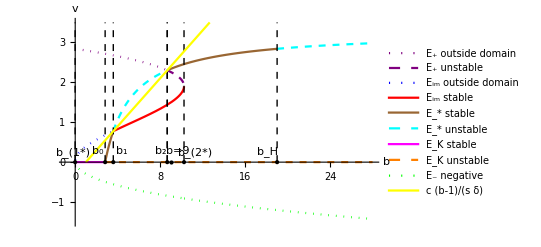

BiifT17.pdf

```mathematica
ClearParameters;
βv=0.16; βy=0.48;K=1;b=9;γ=1;λ=0.36;β=0.11;δ=0.2;βz=0.6; c=0.036;ϵ=0;
Print["{b_(2*),b_(1*)}=",{b/.solb[[1]],b/.solb[[2]]} ,", and b_0=",b0, "  , b_H=",bH,   
 " ,b1=", bnn[[1]],   ", b2=", bnn[[2]]]
Clear["b"];
vs=(((-1+b) β-δ) λ)/(β ((-1+b) β+δ λ))(*v of E* *  ****);
bL=28; max=3.5;bmin=-0.9;
lin1=Line[{{ bc1,0},{ bc1,max}}];
li1=Graphics[{Thick,Black,Dashed,lin1}];
lin2=Line[{{ bc2,0},{ bc2,max}}];
li2=Graphics[{Thick,Black,Dashed,lin2}];
lin3=Line[{{ b0,0},{ b0,max}}];
li3=Graphics[{Thick,Black,Dashed,lin3}];
linH=Line[{{ bH,0},{ bH,max}}];
liH=Graphics[{Thick,Black,Dashed,linH}];
linb1=Line[{{ bnn[[1]],0},{ bnn[[1]],max}}];
lib1=Graphics[{Thick,Black,Dashed,linb1}];
linb2=Line[{{ bnn[[2]],0},{ bnn[[2]],max}}];
lib2=Graphics[{Thick,Black,Dashed,linb2}];
linb9=Line[{{ 9,0},{9,max}}];
lib9=Graphics[{Thick,Black,Dashed,linb2}];
pn=Plot[{vn},{b,0,bL},PlotStyle->{Green,Dotted},PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_- negative"}];
p0=Plot[0,{b,0,bL},PlotStyle->{Brown,Thick},PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_0 saddle point"}];
ppa=Plot[{vp},{b,0, bnn[[2]]},PlotStyle->{Purple,Dotted},PlotRange->{{bmin,bL},{-2,max}},
PlotLegends->{"E_+ outside domain"}];
ppb=Plot[{vp},{b,bnn[[2]], bL},PlotStyle->{Purple,Thick,Dashed},
PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_+ unstable"}];
pi1=Plot[{vi},{b,0,bnn[[1]]},PlotStyle->{Blue,Dotted},
PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_im outside domain"}];
pi2=Plot[{vi},{b,bnn[[1]],bL},PlotStyle->{Red,Thick},
PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_im stable"}];
pi3=Plot[{vi},{b,bnn[[2]],bL},PlotStyle->{Blue,Thick,Dashed},
PlotRange->{{bmin,bL},{-2,max}}(*,PlotLegends->{"E_i unstable"}*)];
ps1=Plot[{vs},{b,b0,bnn[[1]]},PlotStyle->{Brown,Thick},
PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_* stable"}];
ps2=Plot[{vs},{b,bnn[[1]],bnn[[2]]},PlotStyle->{Cyan,Thick,Dashed},
PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_* unstable"}];
ps3=Plot[{vs},{b,bnn[[2]],bH},PlotStyle->{Brown,Thick},
PlotRange->{{bmin,bL},{0,max}}(*,PlotLegends->{"E_* stable"}*)];
ps4=Plot[{vs},{b,bH,bL},PlotStyle->{Cyan,Thick,Dashed},
PlotRange->{{bmin,bL},{-2,max}}(*,PlotLegends->{"E_* unstable"}*)];
pdf1=Plot[{0},{b,0,b0},PlotStyle->{Magenta, Thick},
PlotRange->{{bmin,bL},{0,max}},PlotLegends->{"E_K stable"}];
pdf2=Plot[{0},{b,b0,bL},PlotStyle->{Orange, Thick,Dashed},
PlotRange->{{bmin,bL},{0,max}},PlotLegends->{"E_K unstable"}];
pvmax=Plot[{c (b-1)/(βz δ)(*,(λ(1-c/βz))/β*)},{b,0,bL},PlotStyle->{Yellow},
PlotRange->{{0,bL},{0,max}},
PlotLegends->{"c (b-1)/(s δ)"}];

bifT=Show[{ppa,ppb,pi1,pi2,ps1,ps2,ps3,ps4,pdf1,pdf2,pn,li1,li2,li3,
lib2,lib1,lib9,pvmax,liH},AxesLabel->{"b","v"},PlotRange->{{bmin,bL},{-3/2,max}},
Epilog->{Text["b_(1*)",Offset[{-2,10},{ bc1,0}]],{PointSize[Large],
Style[Point[{ bc1,0}],Purple]},
Text["b_(2*)",Offset[{11,10},{ bc2,0}]],{PointSize[Large],Style[Point[{ bc2,0}],Yellow]},
Text["b_0",Offset[{-7,11},{ b0,0}]],{PointSize[Large],Style[Point[{ b0,0}],Black]},
Text["b_H",Offset[{-10,11},{ bH,0}]],{PointSize[Large],Style[Point[{ bH,0}],Green]},
Text["b_1",Offset[{8,11},{ bnn[[1]],0}]],{PointSize[Large],Style[Point[{ bnn[[1]],0}],Pink]},
Text["b_2",Offset[{-7,11},{ bnn[[2]],0}]],{PointSize[Large],Style[Point[{ bnn[[2]],0}],Red]},
Text["b=9",Offset[{7,11},{9,0}]],{PointSize[Large],Style[Point[{ 9,0}],Brown]}}]
Export["BiifT17.pdf",bifT]
```

Numerical solution of the stability (Bifurcation diagram) wrt v:

```mathematica
(*Checks on the stability of the fixed points**)
Print["Eigenvalues of E*:"]
Print["E* between b0 and b1"]
Eigenvalues[jacEs1]/.b->3//N
Print["E* between b1 and b2"]
Eigenvalues[jacEs1]/.b->5//N
Print["E* between b2 and b2*"]
Eigenvalues[jacEs1]/.b->9.5//N
Print["E* between b2* and bH"]
Eigenvalues[jacEs1]/.b->15//N
Print["E* after bH"]
Eigenvalues[jacEs1]/.b->25//N
Print["Eigenvalues of Eim:"]
Print["Eim between 0 and b1"]
Chop[Eigenvalues[JEi]/.b->2//N]
Print["E* between b1 and b2*"]
Chop[Eigenvalues[JEi]/.b->9//N]
Print["Eigenvalues of E+:"]
Print["Eim between 0 and b2"]
Chop[Eigenvalues[JEp]/.b->2//N]
Print["E* between b2 and b2*"]
Chop[Eigenvalues[JEp]/.b->9//N]
```

Eigenvalues of E*:

E* between b0 and b1

{-0.0225504,-1.29942,-0.311695,-0.0161607}

E* between b1 and b2

{0.0100227,-1.26091,-0.0763636-0.159107 ⅈ,-0.0763636+0.159107 ⅈ}

E* between b2 and b2*

{-0.0022767,-1.25014,-0.0251954-0.21128 ⅈ,-0.0251954+0.21128 ⅈ}

E* between b2* and bH

{-0.0126814,-1.24799,-0.00652554-0.223959 ⅈ,-0.00652554+0.223959 ⅈ}

E* after bH

{-0.0212776,-1.24705,0.00572283-0.230932 ⅈ,0.00572283+0.230932 ⅈ}

Eigenvalues of Eim:

Eim between 0 and b1

{-1.00272,-0.249728,-0.0735624,0.0456119}

E* between b1 and b2*

{-1.69849,-0.00803072,-0.076539-0.209952 ⅈ,-0.076539+0.209952 ⅈ}

Eigenvalues of E+:

Eim between 0 and b2

{-0.559828,-0.123746,0.053141-0.0959514 ⅈ,0.053141+0.0959514 ⅈ}

E* between b2 and b2*

{-1.29833,0.000834552,-0.0332218-0.21255 ⅈ,-0.0332218+0.21255 ⅈ}

(x-b)-Bifurcation diagram :

{b_(2*),b_(1*)}={10.2462,-0.00697038}, and b_0=2.81818  , b_H=19.0121 ,b1=3.58676, b2=8.66779

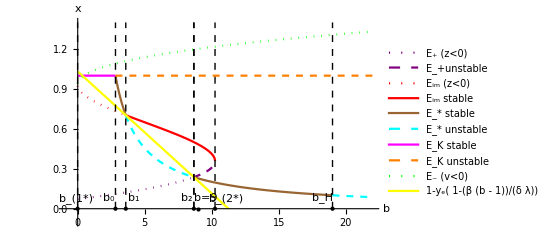

bifx.pdf

```mathematica
Clear["K"];
K=1;
Print["{b_(2*),b_(1*)}=",{b/.solb[[1]],b/.solb[[2]]} ,", and b_0=",b0, "  , b_H=",bH,   
 " ,b1=", bnn[[1]],   ", b2=", bnn[[2]]]
Clear["b"];
xs=EsS[[1]](*x of E* *  ****);
bL=22; max=1.4;bmin=-0.9;
lin1=Line[{{ bc1,0},{ bc1,max}}];
li1=Graphics[{Thick,Black,Dashed,lin1}];
lin2=Line[{{ bc2,0},{ bc2,max}}];
li2=Graphics[{Thick,Black,Dashed,lin2}];
lin3=Line[{{ b0,0},{ b0,max}}];
li3=Graphics[{Thick,Black,Dashed,lin3}];
linH=Line[{{ bH,0},{ bH,max}}];
liH=Graphics[{Thick,Black,Dashed,linH}];
linb1=Line[{{ bnn[[1]],0},{ bnn[[1]],max}}];
lib1=Graphics[{Thick,Black,Dashed,linb1}];
linb2=Line[{{ bnn[[2]],0},{ bnn[[2]],max}}];
lib2=Graphics[{Thick,Black,Dashed,linb2}];
linb9=Line[{{ 9,0},{9,max}}];
lib9=Graphics[{Thick,Black,Dashed,linb2}];
(*pn=Plot[{x/.xee[[1]]},{b,0,b0},PlotStyle->{Purple,Dotted,Thick},PlotRange->{{bmin,bL},{-2,max}}];*)
pn1=Plot[{x/.xee[[1]]},{b,0,bnn[[2]]},PlotStyle->{Purple,Dotted,Thick},PlotRange->{{bmin,bL},{-2,max}},
PlotLegends->{"E_+ (z<0)"}];
pn2=Plot[{x/.xee[[1]]},{b,bnn[[2]],bL},PlotStyle->{Purple,Dashed,Thick},PlotRange->{{bmin,bL},{-2,max}},
PlotLegends->{"E_+unstable"}];
p0=Plot[0,{b,0,bL},PlotStyle->{Brown,Thick},PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_0 saddle point"}];
ppa=Plot[{x/.xee[[2]]},{b,0, bL},PlotStyle->{Green,Dotted},PlotRange->{{bmin,bL},{-2,max}},
PlotLegends->{"E_- (v<0)"}];
pi1=Plot[{x/.xee[[3]]},{b,0,bnn[[1]]},PlotStyle->{Red,Dotted},
PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_im (z<0)"}];
pi2=Plot[{x/.xee[[3]]},{b,bnn[[1]],bL},PlotStyle->{Red,Thick},
PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_im stable"}];
ps1=Plot[{xs},{b,b0,bnn[[1]]},PlotStyle->{Brown,Thick},
PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_* stable"}];
ps2=Plot[{xs},{b,bnn[[1]],bnn[[2]]},PlotStyle->{Cyan,Thick,Dashed},
PlotRange->{{bmin,bL},{-2,max}},PlotLegends->{"E_* unstable"}];
ps3=Plot[{xs},{b,bnn[[2]],bH},PlotStyle->{Brown,Thick},
PlotRange->{{bmin,bL},{0,max}}(*,PlotLegends->{"E_* stable"}*)];
ps4=Plot[{xs},{b,bH,bL},PlotStyle->{Cyan,Thick,Dashed},
PlotRange->{{bmin,bL},{-2,max}}(*,PlotLegends->{"E_* unstable"}*)];
pdf1=Plot[K,{b,0,b0},PlotStyle->{Magenta, Thick},
PlotRange->{{bmin,bL},{0,max}},PlotLegends->{"E_K stable"}];
pdf2=Plot[K,{b,b0,bL},PlotStyle->{Orange, Thick,Dashed},
PlotRange->{{bmin,bL},{0,max}},PlotLegends->{"E_K unstable"}];
pxmax=Plot[{1-ye-β/λ (ye (b-1)/δ)},{b,0,bL},PlotStyle->{Yellow},
PlotRange->{{0,bL},{0,max}},
PlotLegends->{"1-y_e( 1-(β  (b - 1))/(δ λ))"}];

bifx=Show[{pn1,pn2,pi1,pi2,ps1,ps2,ps3,ps4,pdf1,pdf2,ppa,pxmax,li1,li2,li3,
lib2,lib1,lib9,liH},AxesLabel->{"b","x"},PlotRange->{{bmin,bL},{-0.1,max}},
Epilog->{Text["b_(1*)",Offset[{-2,10},{ bc1,0}]],{PointSize[Large],
Style[Point[{ bc1,0}],Purple]},
Text["b_(2*)",Offset[{11,10},{ bc2,0}]],{PointSize[Large],Style[Point[{ bc2,0}],Yellow]},
Text["b_0",Offset[{-7,11},{ b0,0}]],{PointSize[Large],Style[Point[{ b0,0}],Black]},
Text["b_H",Offset[{-10,11},{ bH,0}]],{PointSize[Large],Style[Point[{ bH,0}],Green]},
Text["b_1",Offset[{8,11},{ bnn[[1]],0}]],{PointSize[Large],Style[Point[{ bnn[[1]],0}],Pink]},
Text["b_2",Offset[{-7,11},{ bnn[[2]],0}]],{PointSize[Large],Style[Point[{ bnn[[2]],0}],Red]},
Text["b=9",Offset[{7,11},{9,0}]],{PointSize[Large],Style[Point[{ 9,0}],Brown]}}]
Export["bifx.pdf",bifx]
```

Bifurcation diagram of codimension 2:

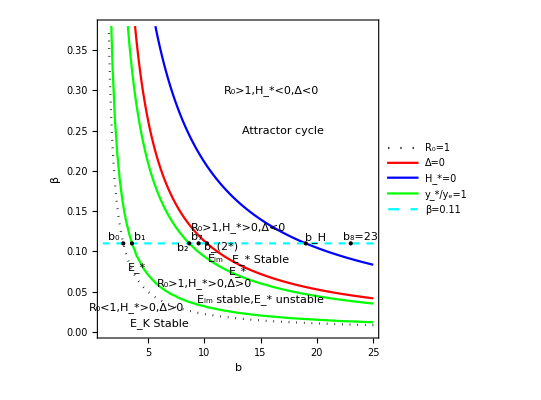

map4.pdf

```mathematica
Clear["b"];
Clear["β"];
(*Here we modified a slightly the values from FindInstance when Tr[jacEs]>0*)
(*λ=1;δ=0.2;βy=0.48;βv=0.16;βz=28;c=1;γ=1;K=1; *)

bm=1; bM=25; ym=0; yM=0.38;
trEp=Tr[JEp];
trEim=Tr[JEi];
detEs=Det[jacEs1];

R1=Style[Text["R_0>1,H_*<0,Δ<0",{16,0.30}],13];
R1a=Style[Text["Attractor cycle",{17,0.25}],13];
R2=Style[Text["R_0>1,H_*>0,Δ<0",{13,0.13}],10];
R2a=Style[Text["E_* Stable",{15,0.09}],10];
RIII=Style[Text["R_0>1,H_*>0,Δ>0",{10,0.06}],10];
RIIIa=Style[Text["E_im stable,E_* unstable",{15,0.04}],10];
RII=Style[Text["E_*",{4,0.08}],10];
RI=Style[Text["E_K Stable",{6,0.01}],10];
RIa=Style[Text["R_0<1,H_*>0,Δ>0",{4,0.03}],10];
Rbi=Style[Text["E_im",{11,0.09}],9];
Rbia=Style[Text["E_*",{13,0.075}],9];

pt0s=Text["b_0",Offset[{-10,6},{b0/.β->0.11,0.11}]];
pt0={PointSize[Medium],Style[Point[{b0/.β->0.11,0.11}],Black]};
ptHs=Text["b_H",Offset[{10,6},{bH,0.11}]];
ptH1={PointSize[Medium],Style[Point[{bH,0.11}],Black]};
ptb2as=Text["b_(2*)",Offset[{14,-3},{bc2/.β->0.11,0.11}]];
ptb2a={PointSize[Medium],Style[Point[{bc2/.β->0.11,0.11}],Black]};
ptb2bs=Text["b_2",Offset[{-6,-5},{bnn[[2]],0.11}]];
ptb2b={PointSize[Medium],Style[Point[{bnn[[2]],0.11}],Black]};
ptb1s=Text["b_1",Offset[{8,6},{bnn[[1]],0.11}]];
ptb1={PointSize[Medium],Style[Point[{bnn[[1]],0.11}],Black]};
ptbas=Text["b_7",Offset[{-2,6},{9.5,0.11}]];
ptba={PointSize[Medium],Style[Point[{9.5,0.11}],Yellow]};
ptbbs=Text["b_8=23",Offset[{10,6},{23,0.11}]];
ptbb={PointSize[Medium],Style[Point[{23,0.11}],Red]};
epi={R1,R1a,R2,R2a,RIII,RIIIa,RII,RI,RIa,Rbi,Rbia,pt0s,pt0,ptHs,ptH1,ptb2as,ptb2a,ptb2bs,ptb2b,
ptbas,ptba,ptbbs,ptbb,ptb1s,ptb1};

pR0=ContourPlot[R0==1,{b,bm,bM},{β,ym,yM},ContourStyle->{Black,Dotted},
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"R_0=1"}];
(*ptrEs=ContourPlot[Tr[jacEs]==0,{b,bm,bM},{β,ym,yM},ContourStyle->{Green,Bold},
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"Tr[J(E_*)]=0"}];*)
 pphi=ContourPlot[H2(*or ϕb*)==0,{b,bm,bM},{β,ym,yM},ContourStyle->{Blue,Bold},PlotPoints -> 180,
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"H_*=0"}];
 pdetEs=ContourPlot[detEs==0,{b,bm,bM},{β,ym,yM},ContourStyle->{Green,Bold},
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"Det[J(E_*)]=0"}];
  pdis=ContourPlot[Dis==0,{b,bm,bM},{β,ym,yM},ContourStyle->{Red,Thick},PlotPoints->180,
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"Δ=0"}];
(*ptrEi=ContourPlot[trEim==0,{b,bm,bM},{β,ym,yM},ContourStyle->{Red,Dashed},PlotPoints -> 180,
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"Tr[J(E_im)]=0"}];*)
 pbeta=ContourPlot[β==0.11,{b,bm,bM},{β,ym,yM},ContourStyle->{Cyan,Dashed},
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"β=0.11"}];
 ppar=ContourPlot[ EsS[[2]]/ye==1,{b,bm,bM},{β,ym,yM},ContourStyle->{Green,Thick},
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"y_*/y_e=1"}];


 
 peq={pR0,pdis,pphi,ppar(*pdetEs,ptrEi*)(*ptrEs,*),pbeta};
pcut=Show[peq,Epilog->epi]
Export["map4.pdf",pcut]
```

```mathematica
(***Some checks***)
(*For Ein**)
Chop[Evaluate[xee[[3]]/.b->2]]//N
Chop[Evaluate[zee/.vee/.xee[[3]]/.y->ye/.b->2]]//N
Chop[vee/.zee/.xee[[3]]/.y->ye/.b->2]//N
(*For E+**)
Chop[Evaluate[xee[[1]]/.b->3]]//N
Chop[zee/.vee/.xee[[1]]/.y->ye/.b->3]//N
Chop[vee/.zee/.xee[[1]]/.y->ye/.b->3]//N
```

{x→0.768927}

{z→-0.439052}

{v→0.559875}

{x→0.113348}

{z→-0.912093}

{v→2.70541}

```mathematica
Chop[Evaluate[xee[[2]]/.b->6]]//N
zee/.vee/.xee[[2]]/.y->ye/.b->6//N
vee/.zee/.xee[[2]]/.y->ye/.b->6//N
```

{x→1.15674}

{z→-5.21725+3.87119×10^-16 ⅈ}

{v→-0.709334-9.08364×10^-17 ⅈ}

Parametric plots at the intervals of stability:

When b2<b=9<b2*:

E*{0.227273,0.0584416,2.33766}

E+={0.249944,0.06,2.25837,0.072607}

Ei={0.483284,0.06,1.49471,0.675711}

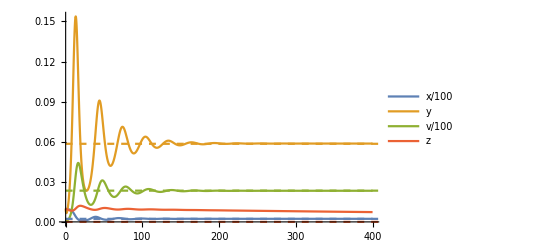

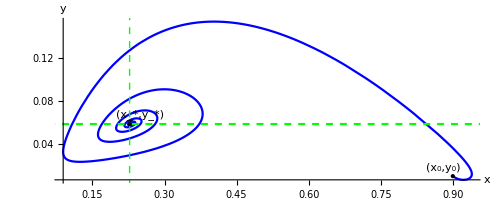

pb9.pdf

Dyni22.pdf

Dyns22.pdf

```mathematica
b=9;
Print["E*",Es=EsS//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi//N]]

X={x,y,v,z};
Xt=Map[#[t]&,X ];
Thread[X->Xt];
dynt=dyn/.Thread[X->Xt];
x1=dynt[[1]] ;
y1=dynt[[2]];
v1=dynt[[3]];
z1=dynt[[4]];
x0=0.9; y0=0.01;v0=0.01;z0=0.01;
ode3={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x0,y[0]==y0,v[0]==v0,z[0]==z0};
sol22=NDSolve[ode3,{x,y,v,z},{t,0,400}];
pdy2=Plot[{x[t]/100/. sol22,y[t]/. sol22,v[t]/100/. sol22,z[t]/. sol22},{t,0,400},
PlotLegends->{"x/100","y","v/100","z"}];
pEs2=Plot[{x/100/.x->Es[[1]],y/.y->Es[[2]],v/100/.v->Es[[3]],z/.z->0},{t,0,1000},
PlotStyle->{Dashed}];
pEi2=Plot[{x/100/.x->Ei[[1]],y/.y->Ei[[2]],v/100/.v->Ei[[3]],z/.z->Ei[[4]]},{t,0,1000},
PlotStyle->{Dashed}];
Dyni22=Show[pdy2,pEi2];
Dyns22=Show[pdy2,pEs2]

(*****¨Parametric plot conditions***)
ppb9=ParametricPlot[{  x[t],(y[t])}/.sol22,{t,0,200}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue}];
py9=Plot[(y/.y->Es[[2]]),{t,0,800},PlotStyle->{Dashed,Green}];
pb9=Show[{ppb9,py9, Graphics[{Green,Dashed,Line[{{x/.x->Es[[1]],0},{x/.x->Es[[1]],1}}]}] },
Epilog->{{Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Es[[1]]),(y/.y->Es[[2]])}]],{PointSize[Large],
Style[Point[{(x/.x->Es[[1]]),(y/.y->Es[[2]])}],Black]}},{PointSize[Large],Point[{x0,y0}]},
Text["(x_0,y_0)",Offset[{-10,8},{x0,y0}]]}]
Export["pb9.pdf",pb9]
Export["Dyni22.pdf",Dyni22]
Export["Dyns22.pdf",Dyns22]
```

When b2<b=9<b2*  and different initial values :

E*{0.227273,0.0584416,2.33766}

E+={0.249944,0.06,2.25837,0.072607}

Ei={0.483284,0.06,1.49471,0.675711}

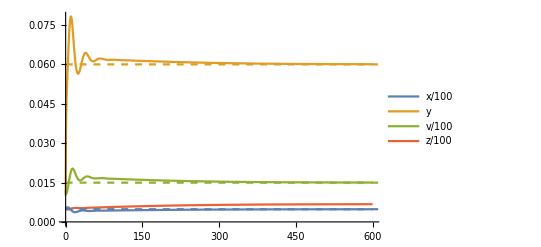

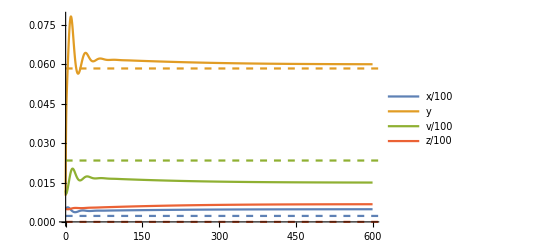

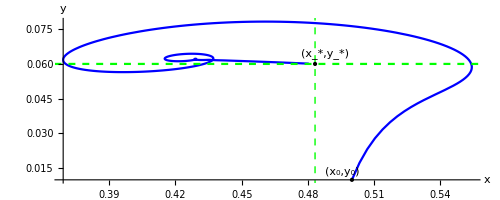

pb9i.pdf

Dyni22b.pdf

```mathematica
b=9;
Print["E*",Es=EsS//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi//N]]

X={x,y,v,z};
Xt=Map[#[t]&,X ];
Thread[X->Xt];
dynt=dyn/.Thread[X->Xt];
x1=dynt[[1]] ;
y1=dynt[[2]];
v1=dynt[[3]];
z1=dynt[[4]];
x0=0.5; y0=0.01;v0=1.2;z0=0.5;
ode3={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x0,y[0]==y0,v[0]==v0,z[0]==z0};
sol22=NDSolve[ode3,{x,y,v,z},{t,0,1000}];
pdy2=Plot[{x[t]/100/. sol22,y[t]/. sol22,v[t]/100/. sol22,z[t]/100/. sol22},{t,0,600},
PlotLegends->{"x/100","y","v/100","z/100"}];
pEs2=Plot[{x/100/.x->Es[[1]],y/.y->Es[[2]],v/100/.v->Es[[3]],z/.z->0},{t,0,1000},
PlotStyle->{Dashed}];
pEi2=Plot[{x/100/.x->Ei[[1]],y/.y->Ei[[2]],v/100/.v->Ei[[3]],z/.z->Ei[[4]]},{t,0,1000},
PlotStyle->{Dashed}];
Dyni22b=Show[pdy2,pEi2]
Dyns22=Show[pdy2,pEs2]

(*****¨Parametric plot conditions***)
ppb9=ParametricPlot[{  x[t],(y[t])}/.sol22,{t,0,500}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue}];
py9=Plot[(y/.y->Ei[[2]]),{t,0,800},PlotStyle->{Dashed,Green}];
pb9i=Show[{ppb9,py9, Graphics[{Green,Dashed,Line[{{x/.x->Ei[[1]],0},{x/.x->Ei[[1]],1}}]}] },
Epilog->{{Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Ei[[1]]),(y/.y->Ei[[2]])}]],{PointSize[Large],
Style[Point[{(x/.x->Ei[[1]]),(y/.y->Ei[[2]])}],Black]}},{PointSize[Large],Point[{x0,y0}]},
Text["(x_0,y_0)",Offset[{-10,8},{x0,y0}]]}]
Export["pb9i.pdf",pb9i]
Export["Dyni22b.pdf",Dyni22b]
```

When b2<b=10<b2*:

E*{0.213904,0.0562055,2.38873}

E+={0.273477,0.06,2.18135,0.195148}

Ei={0.453156,0.06,1.59331,0.67437}

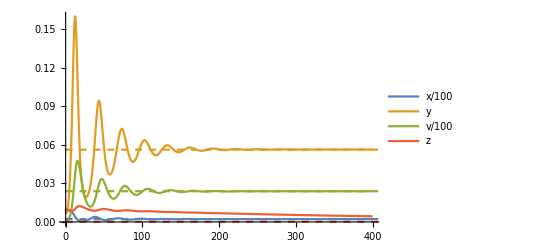

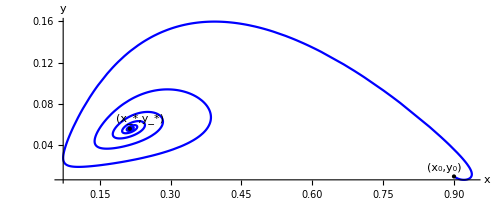

pb10.pdf

Dyns22T.pdf

```mathematica
Clear["b"];
b=9.5;
Print["E*",Es=EsS//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi//N]]

X={x,y,v,z};
Xt=Map[#[t]&,X ];
Thread[X->Xt];
dynt=dyn/.Thread[X->Xt];
x1=dynt[[1]] ;
y1=dynt[[2]];
v1=dynt[[3]];
z1=dynt[[4]];
x0=0.9; y0=0.01;v0=0.01;z0=0.01;
ode3={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x0,y[0]==y0,v[0]==v0,z[0]==z0};
sol22=NDSolve[ode3,{x,y,v,z},{t,0,400}];
pdy2=Plot[{x[t]/100/. sol22,y[t]/. sol22,v[t]/100/. sol22,z[t]/. sol22},{t,0,400},
PlotLegends->{"x/100","y","v/100","z"}];
pEs2=Plot[{x/100/.x->Es[[1]],y/.y->Es[[2]],v/100/.v->Es[[3]],z/.z->0},{t,0,1000},
PlotStyle->{Dashed}];
Dyns22=Show[pdy2,pEs2]

(*****¨Parametric plot conditions***)
ppb10=ParametricPlot[{  x[t],(y[t])}/.sol22,{t,0,200}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue}];
py10=Plot[(y/.y->Es[[2]]),{t,0,800},PlotStyle->{Dashed,Green}];
pb10=Show[{ppb10},Epilog->{{Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Es[[1]]),
(y/.y->Es[[2]])}]],{PointSize[Large],Style[Point[{(x/.x->Es[[1]]),(y/.y->Es[[2]])}],Black]}},
{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{-10,8},{x0,y0}]]}]

Export["pb10.pdf",pb10]
Export["Dyns22T.pdf",Dyns22]
```

E*{0.213904,0.0562055,2.38873}

E+={0.273477,0.06,2.18135,0.195148}

Ei={0.453156,0.06,1.59331,0.67437}

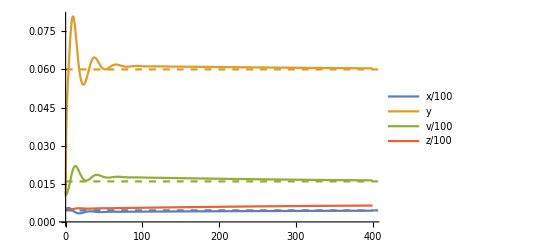

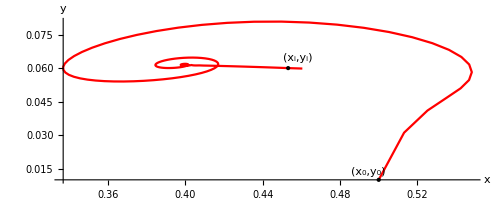

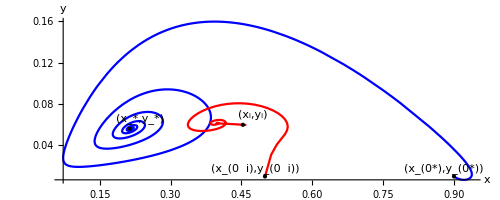

pp10si.pdf

pb10i.pdf

Dyni22T.pdf

```mathematica
Print["E*",Es=EsS//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi//N]]

X={x,y,v,z};
Xt=Map[#[t]&,X ];
Thread[X->Xt];
dynt=dyn/.Thread[X->Xt];
x1=dynt[[1]] ;
y1=dynt[[2]];
v1=dynt[[3]];
z1=dynt[[4]];
x0=0.5; y0=0.01;v0=1.2;z0=0.5;
ode3={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x0,y[0]==y0,v[0]==v0,
z[0]==z0};
sol22=NDSolve[ode3,{x,y,v,z},{t,0,1000}];
pdy2=Plot[{x[t]/100/. sol22,y[t]/. sol22,v[t]/100/. sol22,z[t]/100/. sol22},{t,0,400},
PlotLegends->{"x/100","y","v/100","z/100"}];
pEi2=Plot[{x/100/.x->Ei[[1]],y/.y->Ei[[2]],v/100/.v->Ei[[3]],z/.z->Ei[[4]]},{t,0,1000},
PlotStyle->{Dashed}];
Dyni22=Show[pdy2,pEi2]

ppb10i=ParametricPlot[{  x[t],(y[t])}/.sol22,{t,0,1900}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Red}];
py10i=Plot[(y/.y->Ei[[2]]),{t,0,800},PlotStyle->{Dashed,Green}];
pb10i=Show[{ppb10i },Epilog->{{Text["(x_i,y_i)",Offset[{10,10},{(x/.x->Ei[[1]]),
(y/.y->Ei[[2]])}]],
{PointSize[Large],Style[Point[{(x/.x->Ei[[1]]),(y/.y->Ei[[2]])}],Black]}},
{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{-10,8},{x0,y0}]]}]
pp10si=Show[{pb10,pb10i},Epilog->{{Text["(x_i,y_i)",Offset[{10,10},{(x/.x->Ei[[1]]),
(y/.y->Ei[[2]])}]],{PointSize[Large],Style[Point[{(x/.x->Ei[[1]]),(y/.y->Ei[[2]])}],Black]}},
{PointSize[Large],Point[{x0,y0}]},Text["(x_(0  i),y_(0  i))",Offset[{-10,8},{x0,y0}]],
{Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Es[[1]]),(y/.y->Es[[2]])}]],{PointSize[Large],
Style[Point[{(x/.x->Es[[1]]),(y/.y->Es[[2]])}],Black]}},{PointSize[Large],Point[{0.9,0.01}]},
Text["(x_(0*),y_(0*))",Offset[{-10,8},{0.9,0.01}]]}]
Export["pp10si.pdf",pp10si]
Export["pb10i.pdf",pb10i]
Export["Dyni22T.pdf",Dyni22]
```

When bH<b=23<b∞:

E*{0.0826446,0.0265046,2.91551}

E+={0.297813+0.339863 ⅈ,0.06,2.1017-1.11228 ⅈ,1.75115+1.463 ⅈ}

Ei={0.297813-0.339863 ⅈ,0.06,2.1017+1.11228 ⅈ,1.75115-1.463 ⅈ}

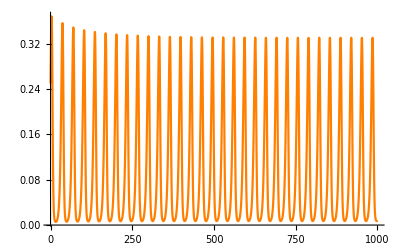

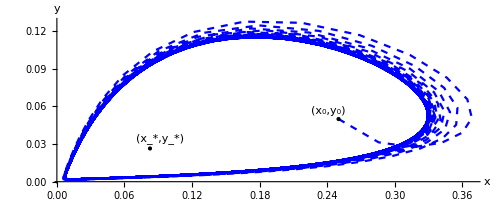

pb23.pdf

DynHI.pdf

```mathematica
Clear["b"]; 
b=23;T=2000;
Print["E*",Es=EsS//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi//N]]
X={x,y,v,z};
Xt=Map[#[t]&,X ];
Thread[X->Xt];
dynt=dyn/.Thread[X->Xt];
x1=dynt[[1]] ;
y1=dynt[[2]];
v1=dynt[[3]];
z1=dynt[[4]];
x01=0.25; y01=0.05;v01=0.01;z01=0.01;
ode5={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x01,y[0]==y01,v[0]==v01,
z[0]==z01};
solHI=NDSolve[ode5,{x,y,v,z},{t,0,T}];
pdyHI1=Plot[{x[t]/. solHI(*,y[t]/. solHI,v[t]/. solHI,z[t]/. solHI*)},{t,0,T/2},PlotStyle->Orange];
DynHI1=Show[pdyHI1,PlotRange->All]

(*****¨Parametric plot conditions***)
ppb23=ParametricPlot[{  x[t],(y[t])}/.solHI,{t,0,T}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue,Dashed}];
NDSolve[{y'[t]==y[t] (x[t]-1),x'[t]==x[t] (2-y[t]),x[0]==1,y[0]==2.7},{x,y},{t,0,10}];
py23=Plot[(y/.y->Es[[2]]),{t,0,400},PlotStyle->{Dashed,Green}];
pb23=Show[{ppb23},Epilog->{{Thick,Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Es[[1]]),
(y/.y->Es[[2]])}]],{PointSize[Large],Style[Point[{(x/.x->Es[[1]]),(y/.y->Es[[2]])}],Green]}},
{PointSize[Large],Point[{x01,y01}]},Text["(x_0,y_0)",Offset[{-10,8},{x01,y01}]]}]
Export["pb23.pdf",pb23]
Export["DynHI.pdf",DynHI]
```

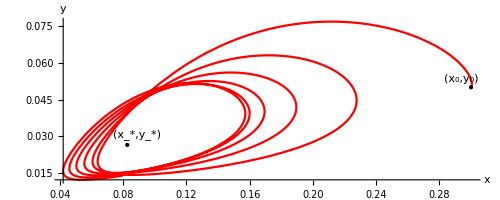

pb23b.pdf

DynHIb.pdf

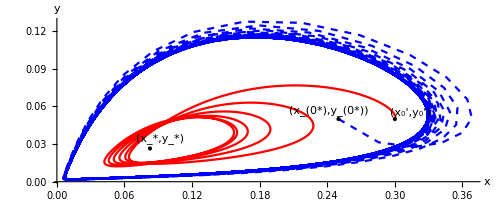

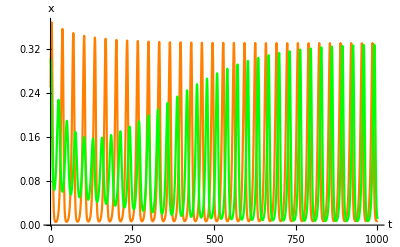

xtH.pdf

pp23s.pdf

```mathematica
x0=0.3; y0=0.05;v0=2;z0=0.5;T=2000;
ode5={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==x0,y[0]==y0,v[0]==v0,z[0]==z0};
solHI=NDSolve[ode5,{x,y,v,z},{t,0,10000}];
pdyHI=Plot[{x[t]/. solHI(*,y[t]/. solHI,v[t]/. solHI,z[t]/. solHI*)},{t,0,T/2},PlotStyle->Green,
AxesLabel->{"t","x"}];
DynHIc=Show[pdyHI,PlotRange->All];
(*New initial conditions**)
ppb23c=ParametricPlot[{  x[t],(y[t])}/.solHI,{t,0,150}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Red}];
pb23c=Show[{ppb23c },Epilog->{{Thick,Text["(x_*,y_*)",Offset[{10,10},
{(x/.x->Es[[1]]),(y/.y->Es[[2]])}]],{PointSize[Large],Style[Point[{(x/.x->Es[[1]]),
(y/.y->Es[[2]])}],Green]}},{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",
Offset[{-10,8},{x0,y0}]]}]
Export["pb23b.pdf",pb23c]
Export["DynHIb.pdf",DynHIc]
pp23cs=Show[{pb23,pb23c},Epilog->{{Thick,Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Es[[1]]),
(y/.y->Es[[2]])}]],{PointSize[Large],Style[Point[{(x/.x->Es[[1]]),(y/.y->Es[[2]])}],Green]}},
{PointSize[Large],Point[{x0,y0}]},Text["(x_0',y_0')",Offset[{16,6},{x0,y0}]],
{PointSize[Large],Point[{x01,y01}]},Text["(x_(0*),y_(0*))",Offset[{-10,8},{x01,y01}]]}]
xtH=Show[{DynHI1,DynHIc},AxesLabel->{"t","x"}]
Export["xtH.pdf",xtH]
Export["pp23s.pdf",pp23cs]
```

Illustration of the limit cycle by combining EcoEvo package with Parametric plot:

EcoEvo Package Version 1.6.4 (November 5, 2021)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0,y→0,v→0,z→0},{x→1.,y→0,v→0,z→0},{x→0.0826446,y→0.0265046,v→2.91551,z→0},{x→0,y→0.06,v→-10.35,z→-2.08333},{x→1.33937,y→0.06,v→-1.30704,z→-8.7697},{x→0.297813+0.339863 ⅈ,y→0.06,v→2.1017-1.11228 ⅈ,z→1.75115+1.463 ⅈ},{x→0.297813-0.339863 ⅈ,y→0.06,v→2.1017+1.11228 ⅈ,z→1.75115-1.463 ⅈ}}

Eigenvalues of E*:{-1.24715,0.00415397+0.230094 ⅈ,0.00415397-0.230094 ⅈ,-0.0200972}

We simulate around

{v→2.91551,z→0,x→0.182645,y→0.0365046}

Final time slice of the cycle is

32.613

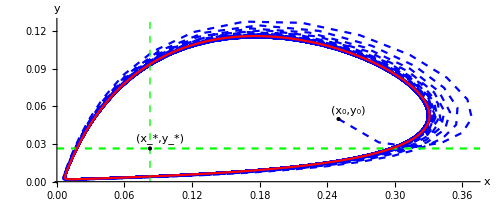

cyH.pdf

```mathematica
<<EcoEvo`
(*EcoEvoDocs;*)
UnsetModel; T=10000;x0=0.9;y0=0.01;
SetModel[{Pop[x]->{Equation:>dyn[[1]],Color->Red},Pop[y]->
{Equation:>(dyn[[2]]),Color->Green},
Pop[v]->{Equation:>(dyn[[3]]),Color->Purple},Pop[z]->{Equation:>(dyn[[4]]),Color->Blue}}]

fpT=SolveEcoEq[]//FullSimplify
Print["Eigenvalues of E*:",EcoEigenvalues[fpT[[3]]]]
Print["We simulate around "]
Esn=RuleListTweak[fpT[[3]],{x,y},{0.1,0.01}]
sol=EcoSim[Esn,T];
psol=PlotDynamics[sol](*Time plot around E* *);

lc=FindEcoCycle[FinalSlice[sol]](*Finding the cycle using time slice*);
Print["Final time slice of the cycle is"]
FinalTime[lc]

pyn=Plot[(y/.fpT[[3,2]]),{t,0,T},PlotStyle->{Dashed,Green}];
cyH=Show[{ppb23,pyn, Graphics[{Green,Dashed,
Line[{{x/.fpT[[3,1]],0},{x/.fpT[[3,1]],1}}]}] },RuleListPlot[lc,{x,y},PlotStyle->{Red}],
Epilog->{{Text["(x_*,y_*)",Offset[{10,10},{(x/.fpT[[3,1]]),(y/.fpT[[3,2]])}]],
{PointSize[Large],Style[Point[{(x/.fpT[[3,1]]),(y/.fpT[[3,2]])}],Black]}},
{PointSize[Large],Point[{x01,y01}]},Text["(x_0,y_0)",Offset[{10,8},{x01,y01}]]}]
Export["cyH.pdf",cyH]
```